# Diagnostic Performance vs Latent Dimension

This notebook summarizes diagonal-test performance for ENCA models trained with different latent-space dimensions. For each z dimension, the diagnostic output provides the Pearson correlation and normalized RMSE for each physical parameter. The plots compare correlation with a baseline-corrected performance score, using the prior-mean predictor as the zero-performance reference.

The numerical pairs below are copied from the output of diag_test.py. For each parameter and latent dimension, the first number is the Pearson correlation between true and predicted parameter values, and the second number is RMSE divided by the prior range, reported in percent.

```mathematica
τ6={0.9776,6.1};
T6={0.8528,15.4};
Nd6={0.4464,26.0};
σ6={0.0035,29.3};
Bmax6={0.9367,10.0};
```

```mathematica
τ8={0.9826,5.4};
T8={0.9658,7.7};
Nd8={0.8997,12.5};
σ8={0.0195,29.2};
Bmax8={0.9668,7.3};
```

```mathematica
τ10={0.9840,5.1};
T10={0.9838,5.3};
Nd10={0.9298,10.9};
σ10={-0.0446,29.7};
Bmax10={0.9861,4.8};
```

```mathematica
zDims={6,8,10};
```

```mathematica
paramData=<|"τ"->{τ6,τ8,τ10},"T"->{T6,T8,T10},"Nd"->{Nd6,Nd8,Nd10},"σ"->{σ6,σ8,σ10},"Bmax"->{Bmax6,Bmax8,Bmax10}|>
```

<|τ→{{0.9776,6.1},{0.9826,5.4},{0.984,5.1}},T→{{0.8528,15.4},{0.9658,7.7},{0.9838,5.3}},Nd→{{0.4464,26.},{0.8997,12.5},{0.9298,10.9}},σ→{{0.0035,29.3},{0.0195,29.2},{-0.0446,29.7}},Bmax→{{0.9367,10.},{0.9668,7.3},{0.9861,4.8}}|>

```mathematica
corr[param_]:=paramData[param][[All,1]];

baselineError=1/Sqrt[12];
perf[param_]:=1-(paramData[param][[All,2]]/100)/baselineError;
```

----------------------------------------------------------------------------------------------------------------------------
Performance score 
For each physical parameter, the diagnostic test reports 
normalized RMSE=RMSE/prior range.
Since the parameters are sampled uniformly from their prior intervals, a trivial baseline predictor is one that always predicts the prior mean, i.e. the midpoint of the allowed interval.
For a uniform distribution on[a,b], the standard deviation is (b-a)/Sqrt[12].
Therefore,the normalized RMSE of this trivial mean predictor is $
baselineError=((b-a)/Sqrt[12])/(b-a)=1/Sqrt[12].
We define the baseline-corrected performance score as 
performance=1-normalizedRMSE/baselineError=1-(RMSE/prior range)/(1/Sqrt[12]).

Interpretation:
performance=1  --- perfect prediction,RMSE=0 
performance=0  --- no better than always predicting the prior mean 
performance<0 ---  worse than the prior-mean predictor 

Thus this score measures the fraction of the naive baseline error removed by the encoder.
For example, performance=0.6 means that the model has reduced the RMSE by about 60% relative to always predicting the prior mean.
----------------------------------------------------------------------------------------------------------------------------

```mathematica
dualAxisPlot[title_,corrVals_,perfVals_]:=Module[{perfData,corrData},
perfData=Transpose[{zDims,perfVals}];
corrData=Transpose[{zDims,corrVals}];
ListLinePlot[{perfData,corrData},
Frame->True,Axes->False,
PlotMarkers->Automatic,
PlotStyle->{Blue,Darker[Red]},PlotLegends->Placed[{"1 - (mean) normalized RMSE","mean corr"},Above],FrameLabel->{"latent dimension z","performance score",None,"correlation"},FrameTicks->{{Automatic,Automatic},{Thread[{zDims,zDims}],None}},PlotRange->{{Min[zDims]-1,Max[zDims]+1},{-0.05,1.02}},GridLines->{zDims,Automatic},
ImageSize->520,
PlotLabel->title]]
```

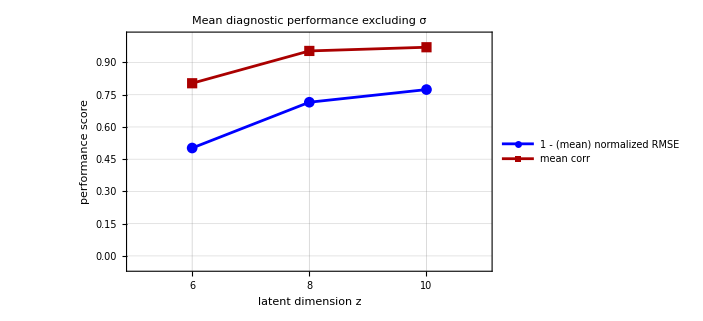

```mathematica
paramsNoSigma={"τ","T","Nd","Bmax"};

meanCorrNoSigma=Mean/@Transpose[corr/@paramsNoSigma];
meanPerfNoSigma=Mean/@Transpose[perf/@paramsNoSigma];

dualAxisPlot["Mean diagnostic performance excluding σ",meanCorrNoSigma,meanPerfNoSigma]
```

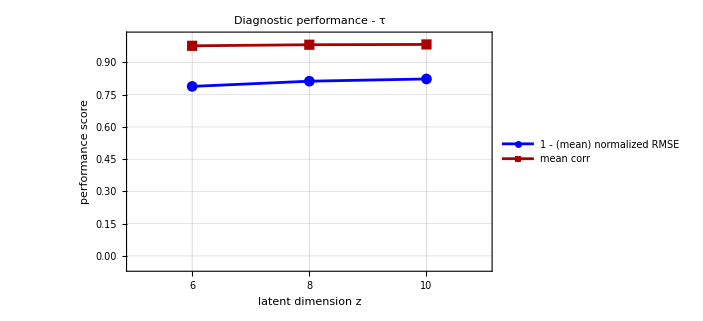

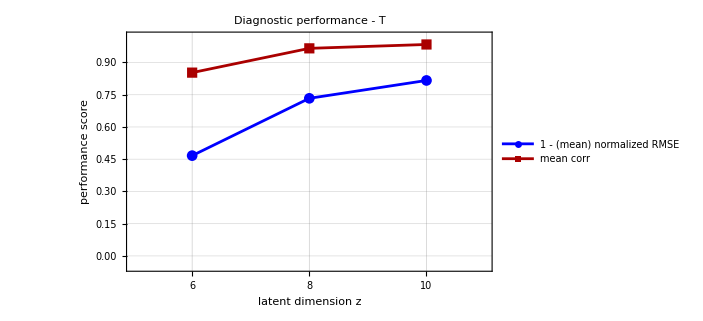

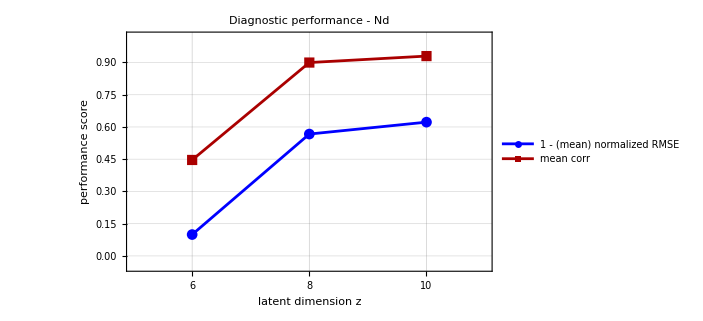

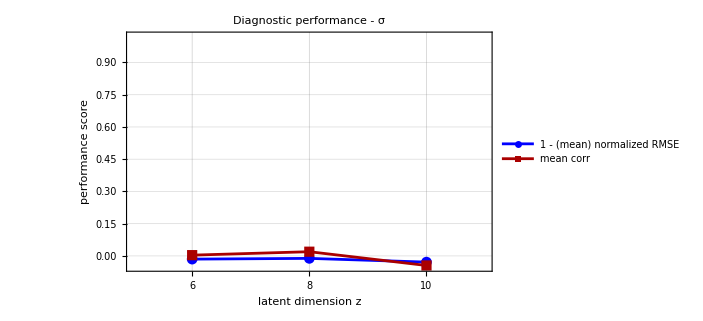

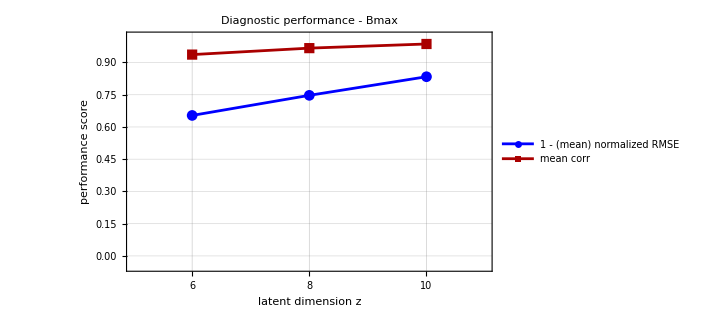

```mathematica
dualAxisPlot["Diagnostic performance - τ",corr["τ"],perf["τ"]]
dualAxisPlot["Diagnostic performance - T",corr["T"],perf["T"]]
dualAxisPlot["Diagnostic performance - Nd",corr["Nd"],perf["Nd"]]
dualAxisPlot["Diagnostic performance - σ",corr["σ"],perf["σ"]]
dualAxisPlot["Diagnostic performance - Bmax",corr["Bmax"],perf["Bmax"]]
```